#### Solow’s model

#### Euler’s method

```mathematica
eulerMethod[f_,t0_,y0_,b_,δ_]:=Module[{y=y0,t,array={y0}},
t=Table[i,{i,t0,b,δ}];Do[y=y+(t⟦i⟧-t⟦i-1⟧)*f[t⟦i-1⟧,y];AppendTo[array,y],{i,2,Length@t}];{t,array}]
```

```mathematica
λ=0.4;
μ=0.7;
s=0.8;
a=3;
α=0.3;
```

```mathematica
f[t_,k_]:=-(λ+μ)k+s a k^α
```

```mathematica
p1=eulerMethod[f,0,3,10,0.01];
p1⟦-1,-1⟧
```

3.04806

#### Classic Runge’s method of order 4

```mathematica
solveDE4order[f_,x_,y_,h_,b_]:=Module[{x0,k1,k2,k3,k4,y0,array={},arrayx={}},
x0=x;
y0=y;
While[x0<b,
k1= f[x0,y0];
k2= f[x0+h/2,y0+h k1/2];
k3= f[x0+h/2,y0+h k2/2];
k4= f[x0+h,y0+h k3];
y0=y0+h(k1+2k2+2k3+k4)/6;
AppendTo[array,y0];
AppendTo[arrayx,x0];
x0+=h];{arrayx,array}]
```

```mathematica
p2=solveDE4order[f,0,5,0.01,10];
p2⟦-1,-1⟧
```

3.04889

```mathematica
ke=(s a/(λ+μ))^(1/(1-α))
```

3.04808

```mathematica
intervals={{0,(α s a/(λ+μ))^(1/(1-α))},{(α s a/(λ+μ))^(1/(1-α)),(s a/(λ+μ))^(1/(1-α))},{( s a/(λ+μ))^(1/(1-α)),10}};
```

```mathematica
p3=solveDE4order[f,0,1.5,0.01,10];
```

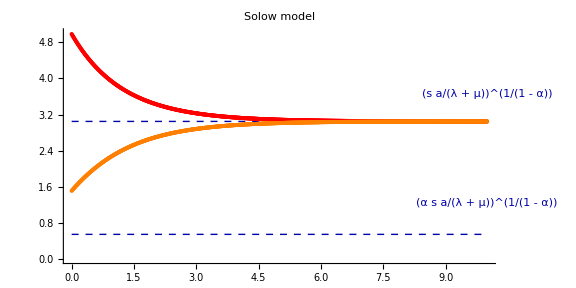

```mathematica
Show[{Graphics[{Red,PointSize[0.005],Point[p2//Transpose],Orange,Point[p3//Transpose]},ImageSize->Large,PlotLabel->"Solow model",PlotRange->{Automatic,{0,5}}],Graphics[{Thick,Dashed,Darker@Blue,Line[{{0,intervals⟦1,2⟧},{10,intervals⟦1,2⟧}}],Inset[Text["(α s a/(λ + μ))^(1/(1 - α))"],{10,intervals⟦1,2⟧+0.7}],Inset[Text["(s a/(λ + μ))^(1/(1 - α))"],{10,intervals⟦2,2⟧+0.6}],Line[{{0,intervals⟦2,2⟧},{10,intervals⟦2,2⟧}}]}]},Axes->True]
```